```mathematica
Clear["Global`*"]
(*Physical constants in cgs units*)
G=6.67 10^-8;  (*Newton's constant in cgs*)
c=3 10^10 ; (*Speed of light in cgs*)
κr=1.6 10^24;
kb=1.38 10^-16;
μ0=0.615;
mp=1.67 10^-24;
(*Stefan-Boltzmann constant in cgs*)
σ=5.67 10^-5;
h=6.63 10^-27;
Msun=2 10^33;

B[Teff_]:=(2 h ν1^3/c^2)/(E^((h ν1)/( kb Teff))-1)
νpeak[Teff_]:=2.82 kb Teff/h


(*Calculates graybody atmosphere using Taka's formalism for a particular Teff and gravity parameter. Free is a flag to switch between the free-free and bound-free opacities*)
GrayBody[Teff_, Qg_, Free_:False]:=Module[{κes, κs, κsb, κsf, ϵs,  ξ, f, x  , K, ϵ, Tp, Ξ, ρp, pr, pg, r},
κes=0.4;
(*Note that the below expression for κs assumes radiation pressure dominance. We also assume solar metallicities*)
κsb=4.7 10^20 √Qg Tp^(-15/4);
κsf=0.04 κsb;
(*If the free-free opacity dominates; Note we assume a H-He atmosphere with solar abundances*)
If[Free, κs= κsf, κs=κsb];
(*κs=1.83 10^9 √Qg(Teff)^(-9/4)*)
ϵs=κs/(κs+κes);
Ξ=(0.873 ϵs^(-1/6))/(1-0.127 ϵs^(5/6))1/(1+(ϵs^-1-1)^(2/3));
r=FindRoot[σ Teff^4 ==Ξ σ Tp^4, {Tp, Teff}];
(*Correction to total flux from scattering*)
Tp=Tp/.r;
x=(1+1/ϵs)^-1;
ξ=(h ν1)/(kb Teff);
f=(ξ)^-3(1-ⅇ^-ξ);
(*Solve cubic equation for the ratio of absorption opacity to scattering opacity*)
K=-1/3+2^(1/3)/(3 (-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))+((-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))/(3 2^(1/3));
(*Estimate density at the base of the photosphere for the peak frequency*)
ρp= (3 c Qg)/(4 (γ) σ Tp^4    κes^2(1+K)K)/.{ν1->νpeak[Teff], γ->4/3};
(*Estimate ratio of gas pressure to radiation pressure*)
pr=(4σ)/(3c)Tp^4;
pg= (ρp kb Tp)/(μ0 mp);
ϵ=(1+1/K)^-1//Simplify;


{pr/pg, Tp, ϵ}
]

PlotSpec[ file_:"fort.14", color_:Black,xrange_:{}, nmu_:10, mu_:1]:=Module[{dat, int, λ, ν, λh, νh, νpeak, imu, peak, prange},
SetDirectory[NotebookDirectory[]];
dat=ReadList[file, Number, RecordLists->True];
(*wavelengths in angstroms + fluxes*)
λh=Extract[dat, Position[dat, x_/;Length[x]==2]];
λh[[All, 2]]=λh[[All,2]] 4π;
νh=λh;
(*Getting frequency information*)
νh[[All,1]]=c/λh[[All, 1]] 10^8;
ν=νh[[All,1]];
peak=ν νh[[All,2]]//Max;
νpeak=ν[[(νh[[All,2]]//Ordering//#[[-1]]&)]];

(*Extract the specific intensities*)
imu=DeleteCases[dat, x_/;Length[x]==2];

imu=imu//Flatten//Partition[#, 2*nmu]&//#[[All, mu]]&;

If[xrange=={}, prange=Automatic, prange=xrange];
ListLogLogPlot[Transpose[{ν, νh[[All,2]] ν}], AxesLabel->{"ν [s^-1]", "ν F_ν [erg cm^-2 s^-1]"},  Joined->True, PlotStyle->Directive[color], PlotRange->{prange, {10^-4 peak , peak}}, PlotRangeClipping->False]



]
Opac[ file_:"fort.85", nd_:70]:=Module[{κ, ν, dat},
SetDirectory[NotebookDirectory[]];
dat=ReadList[file, Number, RecordLists->True];
(*frequencies*)
ν=Extract[dat, Position[dat, x_/;Length[x]==2]];
ν=ν[[All,2]];
κ=DeleteCases[dat,x_/;Length[x]==2]//Flatten//Partition[#, nd]&;
Table[{ν[[i]], κ[[i]]}, {i, 1, Length[ν]}]

]
(*Parses a model atmosphere from a unit 7 input file*)
ParseAtm[file_:"fort.7"]:=Module[{atm, m,nd, blocks},
atm=ReadList[file, Number];
nd=atm[[1]];
blocks=atm[[2]];
atm=atm[[3;;]];
m=atm[[1;;nd]];
atm=atm[[nd+1;;]];
atm=Partition[atm, blocks][[All, 1;;4]];
atm=Flatten/@Transpose[{m, atm}]

]
PlotF[ file_:"fort.13", color_:Black]:=Module[{fluxdat, peak, sed, peakf, peakloc,bad},
(*import data file*)
fluxdat= Import[file, "Table"][[All, 1;;2]];


fluxdat[[All,2]]=4π fluxdat[[All,2]];
sed=Transpose[{fluxdat[[All,1]],fluxdat[[All, 1]]*fluxdat[[All,2]]}];
(*Output is sometimes formatted in such a way that mathematica does not recognize it as a real number*)
bad=DeleteCases[sed, x_/;x[[2]]∈Reals];
sed=Complement[sed, bad];
(*Get location of peak for setting the range of the plot*)
peakloc=sed[[All,2]]//Ordering//#[[-1]]&;
peakf=sed[[peakloc,1]];
peak=sed[[peakloc,2]];

ListLogLogPlot[sed, Joined->True, PlotRange->{{0.1peakf, 10peakf}, {10^-4 peak, peak}}, PlotStyle->Directive[color]]
]
```

```mathematica
atm=ParseAtm["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.7"]
nh=0.74 atm[[All,4]]/mp;
ne=atm[[All,3]];
ne/nh
```

{{0.001,7154.31,1.22492×10^9,3.20121×10^-15,1.50523×10^15},{0.00133785,7180.62,1.69048×10^9,3.94141×10^-15,1.50513×10^15},{0.00178983,7147.85,2.16411×10^9,5.0487×10^-15,1.50503×10^15},{0.00239452,7115.67,2.79908×10^9,6.53435×10^-15,1.50492×10^15},{0.00320351,7084.43,3.64975×10^9,8.52615×10^-15,1.50481×10^15},{0.0042858,7054.35,4.78819×10^9,1.11939×10^-14,1.5047×10^15},{0.00573375,7025.82,6.30925×10^9,1.47625×10^-14,1.50459×10^15},{0.00767087,6999.46,8.33694×10^9,1.95301×10^-14,1.50447×10^15},{0.0102625,6976.14,1.10322×10^10,2.58945×10^-14,1.50436×10^15},{0.0137296,6957.02,1.46036×10^10,3.43883×10^-14,1.50424×10^15},{0.0183681,6943.65,1.9321×10^10,4.57069×10^-14,1.50412×10^15},{0.0245737,6937.96,2.55257×10^10,6.07386×10^-14,1.504×10^15},{0.0328758,6942.08,3.36344×10^10,8.05999×10^-14,1.50388×10^15},{0.0439828,6958.34,4.41443×10^10,1.06646×10^-13,1.50376×10^15},{0.0588423,6989.09,5.76263×10^10,1.40421×10^-13,1.50364×10^15},{0.078722,7036.64,7.46936×10^10,1.83517×10^-13,1.50351×10^15},{0.105318,7103.2,9.59335×10^10,2.37256×10^-13,1.50338×10^15},{0.140899,7190.91,1.2178×10^11,3.02209×10^-13,1.50325×10^15},{0.188502,7302.,1.52322×10^11,3.77623×10^-13,1.50311×10^15},{0.252186,7438.88,1.87098×10^11,4.61124×10^-13,1.50295×10^15},{0.337387,7604.19,2.25058×10^11,5.4924×10^-13,1.50278×10^15},{0.451372,7800.8,2.6498×10^11,6.39083×10^-13,1.50259×10^15},{0.603866,8031.88,3.06408×10^11,7.30673×10^-13,1.50237×10^15},{0.807881,8301.5,3.50676×10^11,8.28587×10^-13,1.50211×10^15},{1.08082,8613.76,4.01351×10^11,9.42169×10^-13,1.5018×10^15},{1.44597,8979.66,4.63627×10^11,1.08375×10^-12,1.50143×10^15},{1.93449,9405.38,5.44241×10^11,1.26886×10^-12,1.50102×10^15},{2.58805,9898.46,6.50869×10^11,1.51465×10^-12,1.50054×10^15},{3.46242,10463.8,7.92267×10^11,1.83925×10^-12,1.50002×10^15},{4.63218,11104.5,9.77095×10^11,2.25396×10^-12,1.49944×10^15},{6.19715,11823.7,1.20813×10^12,2.739×10^-12,1.49881×10^15},{8.29084,12625.5,1.47359×10^12,3.24679×10^-12,1.4981×10^15},{11.0919,13510.8,1.7678×10^12,3.81392×10^-12,1.4973×10^15},{14.8392,14475.5,2.13279×10^12,4.56397×10^-12,1.4964×10^15},{19.8526,15519.,2.61529×10^12,5.58235×10^-12,1.4954×10^15},{26.5598,16646.6,3.22462×10^12,6.87703×10^-12,1.49431×10^15},{35.5329,17867.,3.9372×10^12,8.3928×10^-12,1.49313×10^15},{47.5375,19190.8,4.69222×10^12,9.99907×10^-12,1.49181×10^15},{63.598,20629.5,5.38824×10^12,1.14805×10^-11,1.49031×10^15},{85.0843,22192.3,5.91771×10^12,1.26068×10^-11,1.48852×10^15},{113.83,23883.,6.28165×10^12,1.33756×10^-11,1.48631×10^15},{152.287,25702.9,6.65847×10^12,1.4144×10^-11,1.48351×10^15},{203.736,27660.8,7.12287×10^12,1.49682×10^-11,1.47997×10^15},{272.568,29774.,7.35015×10^12,1.50156×10^-11,1.47538×10^15},{364.655,32034.7,7.6338×10^12,1.52057×10^-11,1.46929×10^15},{487.852,34432.8,8.91326×10^12,1.75946×10^-11,1.46173×10^15},{652.671,36989.,1.12263×10^13,2.21002×10^-11,1.45332×10^15},{873.174,39724.2,1.45117×10^13,2.85406×10^-11,1.44447×10^15},{1168.17,42655.2,1.8866×10^13,3.70879×10^-11,1.43532×10^15},{1562.84,45799.,2.44315×10^13,4.80141×10^-11,1.42589×10^15},{2090.84,49173.2,3.13313×10^13,6.15596×10^-11,1.41611×10^15},{2797.22,52796.5,3.95927×10^13,7.77783×10^-11,1.40583×10^15},{3742.25,56690.,4.89782×10^13,9.61977×10^-11,1.39484×10^15},{5006.56,60876.4,5.88011×10^13,1.15461×10^-10,1.3828×10^15},{6698.01,65377.8,6.79632×10^13,1.3342×10^-10,1.36913×10^15},{8960.91,70210.3,7.56756×10^13,1.48538×10^-10,1.35303×10^15},{11988.3,75380.9,8.24014×10^13,1.61708×10^-10,1.33348×10^15},{16038.5,80891.7,8.97131×10^13,1.76011×10^-10,1.30945×10^15},{21457.1,86745.6,9.89456×10^13,1.94086×10^-10,1.2801×10^15},{28706.3,92948.4,1.10021×10^14,2.15789×10^-10,1.24463×10^15},{38404.7,99501.9,1.21599×10^14,2.38478×10^-10,1.20182×10^15},{51379.6,106394.,1.32302×10^14,2.59449×10^-10,1.14962×10^15},{68738.,113589.,1.41304×10^14,2.7708×10^-10,1.08484×10^15},{91960.9,121015.,1.47807×10^14,2.89812×10^-10,1.00287×10^15},{123030.,128536.,1.52008×10^14,2.98031×10^-10,8.97142×10^14},{164595.,135912.,1.5498×10^14,3.0384×10^-10,7.59009×10^14},{220203.,142721.,1.56609×10^14,3.07015×10^-10,5.76939×10^14},{294597.,148190.,1.57365×10^14,3.08482×10^-10,3.35199×10^14},{394126.,150763.,1.57682×10^14,3.09097×10^-10,1.28798×10^13},{398107.,150767.,1.5768×10^14,3.09094×10^-10,0.}}

{0.863531,0.967929,0.967351,0.966712,0.966038,0.965327,0.964503,0.963358,0.961484,0.958369,0.953966,0.948415,0.941744,0.934151,0.92613,0.918527,0.912511,0.909397,0.910308,0.915662,0.924737,0.93571,0.946372,0.955107,0.961346,0.965435,0.967972,0.969764,0.972113,0.978308,0.995421,1.02426,1.04603,1.0546,1.05728,1.05819,1.05868,1.05902,1.05919,1.05934,1.05985,1.0624,1.07392,1.10468,1.13297,1.14325,1.14638,1.14747,1.14797,1.14833,1.14859,1.14879,1.14901,1.1493,1.14957,1.14975,1.14997,1.15028,1.1505,1.15062,1.15071,1.1508,1.15089,1.15097,1.15104,1.15111,1.15118,1.15123,1.15125,1.15125}

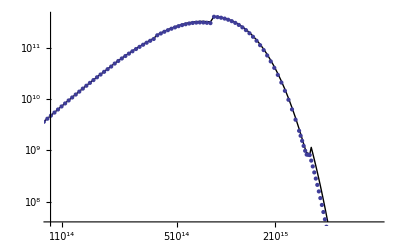

```mathematica
Tp=10^4;
(*Read in  list of opacities*)
o=Opac["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_isot/fort.85"];
χ=o[[All, 2, 1]];
freq=o[[All,1]];
(*Scattering opacity*)
μe=0.74;
σ=μe 0.4;
κ=χ;
(*Pure absorption opacity*)
κ=κ-σ
ϵ=κ;
(*Extinction probability*)
ϵ=κ/(κ+σ);
bb=ν1 B[10^4]/.ν1->freq;
gb=2π  ϵ^(1/2)/(ϵ^(1/2)+1) bb
Show[PlotF["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_isot/fort.13"], ListLogLogPlot[Transpose[{freq, gb}]]]
```

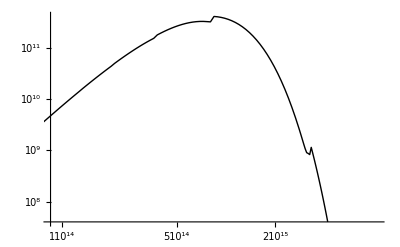

```mathematica
PlotF["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_isot/fort.13"]
```

```mathematica
(*dmtot=5;
m0=-3;
logm=Range[m0, dmtot, 8/69]
m=10^logm//N
ρc=10^-11;
Tp=10^4;
ne=0.74 ρc/mp;
atm=Table[{Tp, ne, ρc,0}, {i, 1 70}]//N;
atm=Flatten/@Transpose[{m, atm}];
(*getting the correct z-coordinate*)
atm[[All, -1]]=atm[[All, 1]]/atm[[All,4]];
Row[m, "    "]
(Map[ScientificForm[#,NumberFormat->(SequenceForm[#1,"E",#3]&) ]&,atm[[All, 2;;]], {2}])//Reverse//TableForm
```

```mathematica
(*atm= ParseAtm["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/tmp/fort.7"];
m=atm[[All, 1]];
o=Opac["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/tmp/fort.85"];
μe=mp atm[[All,3]]/atm[[All,4]];
σ=μe 0.4;
σ=σ[[1]];
(*opacities at various frequencies for the outer-most depth point*)
o1=Transpose[{o[[All, 1]],o[[All,2, 1]]}];
κ=o1[[All, 2]]-σ;
ϵ=κ/(κ+σ);
(*Extinction probabilities at the outer most part of the atmosphere*)
ϵ=Map[If[#<0, 0, #]&, ϵ];
freq=o1[[All,1]];
planck=B[Tp]/.{ν1->freq};
ϵ=ϵ[[2;;]];
planck=planck[[2;;]];
flux=(freq//Differences)ϵ^(1/2)/(ϵ^(1/2)+1)planck//Total;
flux=-2 π flux*)
```

1.56554×10^9

```mathematica
(*dat=ReadList["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40/fort.85", Number, RecordLists->True];
nd=70;
Tp=10600;
(*frequencies*)
ν=Extract[dat, Position[dat, x_/;Length[x]==2]];
ν=ν[[All,2]]
κ=DeleteCases[dat,x_/;Length[x]==2]
κ=κ//Flatten//Partition[#, nd]&
κes=0.4;
tmp= #* Prepend[md//Differences, md[[1]]]&/@κ;
tmp2=FoldList[Plus,0, #]&/@tmp;

tmp3=Nearest[#, 1]&/@tmp2//Flatten;
tmppos=Table[Position[tmp2[[i]], tmp3[[i]]], {i, 1, Length[tmp2]}];
κabs=(Table[Extract[κ[[i]], tmppos [[i]]], {i, 1, Length[tmppos]}]//Flatten)-0.4;
κabs=If[#<0, 0, #]&/@κabs;
ϵ=κabs/(κabs+κes);
gray=Table[{ν[[i]], ϵ[[i]]^(1/2)/(1+ϵ[[i]]^(1/2))B[Tp] ν1/.ν1->ν[[i]]}, {i, 1, Length[ν]}]*)


(*gp2=ListLogLogPlot[gray, Joined->True]*)
```

```mathematica
√(5.01 10^-15)
```

7.07814×10^-8

```mathematica
10^5.6
```

398107.

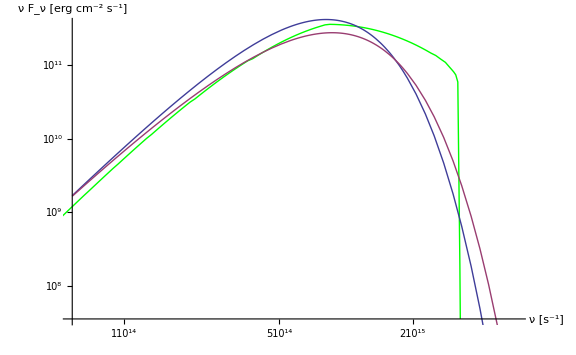

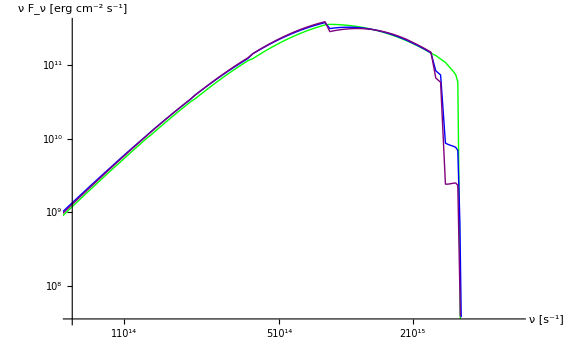

```mathematica
Teff=10^4;
Qg=5.01 10^-13;
GrayBody[Teff, Qg][[1]]//Re
Tp=GrayBody[Teff, Qg][[2]]
ϵ=GrayBody[Teff, Qg][[3]];
bb=π B[Teff] ν1;
gb=π(2 ϵ^(1/2))/(1+ϵ^(1/2)) B[Tp] ν1;
gp=LogLogPlot[ {  bb, gb }, {ν1, 0.1 νpeak[Teff], 10 νpeak[Teff]}]
Show[PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.14",Green, {0.1 νpeak[Teff], 10 νpeak[Teff]}], gp]

Show[PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.14",Green,{0.1 νpeak[Teff], 10 νpeak[Teff]}], PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/lteconv/fort.14", Blue], PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar_gray/t40m56q-143/lteconv/fort.14", Purple]

]

(*fluxdat= Import["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar_isot/fort.13", "Table"][[All, 1;;2]];
fluxdat[[All,2]]=4π fluxdat[[All,2]];
peak=fluxdat[[All, 1]]fluxdat[[All,2]]//Max
Show[gp, ListLogLogPlot[Transpose[{fluxdat[[All,1]], fluxdat[[All,1]] fluxdat[[All, 2]]}], Joined->True, PlotRange->{{ 0.1 νpeak[Teff], 10 νpeak[Teff]}, {10^-4 peak, peak}}], PlotRangeClipping->False]*)
```

```mathematica
Teff=10^4;
Qg=5.01 10^-13;
m=ParseAtm["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.7"][[All,1]]
o=Opac["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.85"]//Reverse;
χ=o//#[[-1,2]]&
ν=o//#[[-1, 1]]&
Transpose[{m, χ}]//ListLogLogPlot
ϵ=GrayBody[Teff, Qg][[3]]/.ν1->ν//Re//ScientificForm
Tp=GrayBody[Teff, Qg][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

19431.7

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

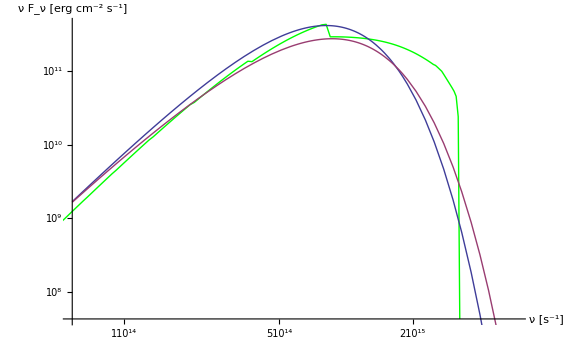

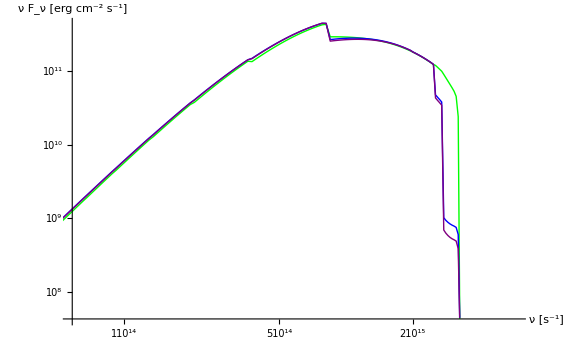

```mathematica
Teff=10^4;
Qg=5.01 10^-15;
Tp=GrayBody[Teff, Qg][[2]]
ϵ=GrayBody[Teff, Qg][[3]];
bb=π B[Teff] ν1;
gb=π(2 ϵ^(1/2))/(1+ϵ^(1/2)) B[Tp] ν1;

Show[PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m36q-123/converged/fort.14",Green, {0.1 νpeak[Teff], 10 νpeak[Teff]}], gp]

Show[PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m36q-123/converged/fort.14",Green,{0.1 νpeak[Teff], 10 νpeak[Teff]}], PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m36q-123/lteconv/fort.14", Blue], PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar_gray/t40m36q-123/lteconv/fort.14", Purple]

]
```

```mathematica
(9/8 ν Σ G (M/R^3)/σ)^0.25/.{Σ->6.2 10^5,  R->126 2 G M/c^2, ν->2 10^17(1.3)^(4/7)}/.{M->10^6 Msun}
```

52009.1